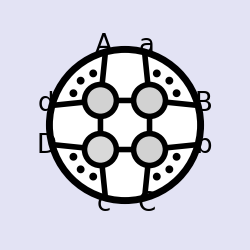
-Graphics-
One-Loop Amplitude Integrands
and Integrals in N=4 SYM
Jacob L. Bourjaily, 2013

```mathematica
n=8;
<<"loop_amplitudes.m";
(* fun *)
ab[___,j_,___,j_,___]:=0;
sortab={i_ab:>Sort[i]Signature[i]/Signature[Sort[i]]};
sortdoubleab={i_doubleab:>Sort[i]Signature[i]/Signature[Sort[i]]};
sortcapinR=R[a__]:>R@@(Replace[List[a],cap[x_,y_]:>cap[ordercup@x,ordercup[y]],{0,Infinity}]);
Qlog[1]:=0;
Dmatrix[0]=0;
doubleab[___,j_,___,j_,___]:=0;
Dmatrix[ab[x__]y_]:=ab[x]Dmatrix[y];
FuseDmatrices:=Expand[#]//.{Dmatrix[i_]Dmatrix[j_]:>Dmatrix@Join[i,j]}&;
abelim={ab[x___,n+1,y___]:>ab[x,n,y]-e ab[x,B,y]};
abtre= ab[aa___,B,bb___]:>ab[aa,n-1,bb]-τ ab[aa,1,bb](ab[n-1,n,2,3]/ab[n,1,2,3])-e ab[aa,2,bb](ab[n-2,n-1,n,1]/ab[n-2,n-1,2,1]);
capexpand = {ab[x___, cap[{a_, b_}, {c__}], y___] :> ab[b, c] ab[x, a, y] + ab[c, a] ab[x, b, y]};
shifexp={ab[x___,shift[y_,z_],w___]:>ab[x,y⟦1⟧,w]+z ab[x,y⟦2⟧,w]};
mom=RandomInteger[{-100,100},{20,4}];
mom1=Table[Binomial[n+i,i],{n,20},{i,0,3}];
neab[exp_]:=exp/.shifexp//.capexpand/.ab[x__]:>Det[mom[[{x}]]];
neab1[exp_]:=exp/.shifexp//.capexpand/.ab[x__]:>Det[mom1[[{x}]]];
todmatrix:=FuseDmatrices[#/.i_R:>(fromRform[n+1][i][[1,1]])Dmatrix[fromRform[n+1][i][[1,2]]]//.shifexp//.capexpand]&;
todmatrixn:=FuseDmatrices[#/.i_R:>(fromRform[n][i][[1,1]])Dmatrix[fromRform[n][i][[1,2]]]//.shifexp//.capexpand]&;
DmatrixEval[fermions__] :={Dmatrix[i_/;Length[i]==Length[{fermions}[[1]]]]:>Product[Det[Array[i[[#1,{fermions}[[l,#2]]]]&,{Length[i],Length[i]}]],{l,1,4}],Dmatrix[i_]:>0};
order[exprn_,option_:1]:=If[option==0,exprn/.{ab[x__]:>Signature[{x}] ab@@Sort[{x}]},Block[{nGuess=Max[Join[{0},Flatten[Apply[List,Cases[exprn,_ab,{0,∞}],{1}]]]],consec,xLike},consec=Partition[Range[nGuess],2,1,1];xLike=Apply[If[Length[Range[#2,#3]]>Length[Range[#4,#1+nGuess]],{#3,#4,#1,#2},{##1}]&,Select[Flatten/@Subsets[consec,{2}],Length[#1∩#1]==4&],{1}];exprn/.{ab[x__]:>If[Length[{x}]==2,(If[Length[#1]==1,Signature[#1[[1]]] Signature[{x}] ab@@#1[[1]],Signature[{x}] ab@@Sort[{x}]]&)[Select[consec,Length[{x}∩#1]==2&,1]],(If[Length[#1]==1,Signature[#1[[1]]] Signature[{x}] ab@@#1[[1]],Block[{xLikeLines=Select[consec,Length[#1∩{x}]==2&],boundaries},If[Length[xLikeLines]==0,Signature[{x}] ab@@Sort[{x}],boundaries=Complement[{x},xLikeLines[[1]]];If[Length[Range[boundaries[[2]],If[xLikeLines[[1,1]]<boundaries[[2]],nGuess,0]+xLikeLines[[1,1]]]]+Length[Range[xLikeLines[[1,2]],If[boundaries[[1]]<xLikeLines[[1,2]],nGuess,0]+boundaries[[1]]]]>Length[Range[boundaries[[1]],If[xLikeLines[[1,1]]<boundaries[[1]],nGuess,0]+xLikeLines[[1,1]]]]+Length[Range[xLikeLines[[1,2]],If[boundaries[[2]]<xLikeLines[[1,2]],nGuess,0]+boundaries[[2]]]],boundaries=Reverse[boundaries];];-Signature[Join[boundaries,xLikeLines[[1]]]] Signature[{x}] ab@@RotateLeft[Join[boundaries,xLikeLines[[1]]]]]]]&)[Select[xLike,Length[#1∩{x}]==4&]]]}]];
twistorSchouten=#1//.{ab[a___,x_,b___,y_,c___] ab[d___,x_,e___,y_,f___]:>Signature[Flatten[{x,y,Sort[{a,b,c}]}]] Signature[{a,x,b,y,c}] Signature[Flatten[{x,y,Sort[{d,e,f}]}]] Signature[{d,x,e,y,f}] ab@@Flatten[{x,y,Sort[{a,b,c}]}] ab@@Flatten[{x,y,Sort[{d,e,f}]}],ab[a___,x_,b___,y_,c___] ab[d___,y_,e___,x_,f___]:>Signature[Flatten[{x,y,Sort[{a,b,c}]}]] Signature[{a,x,b,y,c}] Signature[Flatten[{x,y,Sort[{d,e,f}]}]] Signature[{d,y,e,x,f}] ab@@Flatten[{x,y,Sort[{a,b,c}]}] ab@@Flatten[{x,y,Sort[{d,e,f}]}]}//.{ab[x_,y_,a_,b_] ab[x_,y_,c_,d_]-ab[x_,y_,a_,d_] ab[x_,y_,c_,b_]:>ab[x,y,a,c] ab[x,y,b,d],ab[x_,y_,a_,b_] ab[x_,y_,c_,d_]-ab[x_,y_,a_,c_] ab[x_,y_,b_,d_]:>ab[x,y,a,d] ab[x,y,c,b],ab[x_,y_,a_,b_] ab[x_,y_,c_,d_]+ab[x_,y_,a_,d_] ab[x_,y_,b_,c_]:>ab[x,y,a,c] ab[x,y,b,d],ab[x_,y_,a_,b_] ab[x_,y_,c_,d_]+ab[x_,y_,a_,c_] ab[x_,y_,d_,b_]:>ab[x,y,a,d] ab[x,y,c,b],-ab[x_,y_,a_,b_] ab[x_,y_,c_,d_]-ab[x_,y_,a_,d_] ab[x_,y_,b_,c_]:>-ab[x,y,a,c] ab[x,y,b,d],-ab[x_,y_,a_,b_] ab[x_,y_,c_,d_]-ab[x_,y_,a_,c_] ab[x_,y_,d_,b_]:>-ab[x,y,a,d] ab[x,y,c,b]}&;
twistorSimplify[exprn_,orderQ_:0]:=If[Count[exprn,ab[x_,y_],∞]>0,Simplify[order[exprn]/.Apply[Rule,({#1,twistorSchouten[#1]}&)/@Cases[exprn,ab[x__] ab[y__]-ab[z__] ab[w__]|ab[x__] ab[y__]+ab[z__] ab[w__],{0,∞}],{1}]],order[FullSimplify[If[orderQ==1,order[FullSimplify[order[exprn,0],TransformationFunctions->{Automatic,twistorSchouten}],1],exprn],TransformationFunctions->{Automatic,twistorSchouten}],1]];
toqlog={R[i_,j_,k_,n,n+1]:> Which[i===1&&k===n-1,dlog[ab[X,n-2,n-1]/ab[X,1,2]]Qlog[ab[n-1,n,1,2]/ab[n-1,n,1,j]],k===n-1,dlog[ab[X,i,j]/ab[X,n-2,n-1]]Qlog[ab[n-1,n,1,j]/ab[n-1,n,1,i]],i===1,dlog[ab[X,j,k]/ab[X,1,2]]Qlog[ab[n-1,n,1,k]/ab[n-1,n,1,j]],True,dlog[ab[X,i,j]/ab[X,j,k]]Qlog[ab[n-1,n,1,j]/ab[n-1,n,1,i]]+dlog[ab[X,j,k]/ab[X,i,k]]Qlog[ab[n-1,n,1,k]/ab[n-1,n,1,i]]]};
dab[___,i_,___,i_,___]:=0;
sortdab={i_dab:>(Sort[i] Signature[i])/Signature[Sort[i]]};
dabRcanel[exp_]:=Expand[exp]/.R[x__]dab[y__]:>0/;Sort[{x}]==Sort[{y}];
qlogRcanel[exp_]:=Expand[exp]/.R[x__]Qlog[ab[z__]/ab[y__]]:>0/;Sort[{x}]==Sort[Union[{y},{z}]];
qlogtodab=Qlog[ab[1,i_,n-1,n]/ab[1,j_,n-1,n]]:>dab[1,i,j,n-1,n]/(ab[1,i,n-1,n]ab[1,j,n-1,n]);
Rtodab=R[i_,j_,k_,n,n+1]:>(dab[i,j,k,n,B] ab[i,j,k,n])/(ab[i,j,n,B]ab[j,k,n,B]ab[k,i,n,B]);
dabBexp=dab[x___,B,y___]:>dab[x,n-1,y]-ab[n-1,n,2,3]/ab[n,1,2,3] τ dab[x,1,y]-ab[n-2,n-1,n,1]/ab[n-2,n-1,2,1] e dab[x,2,y];
dabtoqlog={dab[i_,j_,k_,l_,n]:>Which[i===1&&l===n-1,Qlog[ab[n-1,n,1,j]/ab[n-1,n,1,k]]ab[1,j,n-1,n]ab[1,k,n-1,n],l===n-1, Qlog[ab[n-1,n,1,j]/ab[n-1,n,1,i]]ab[n-1,n,1,i]ab[n-1,n,j,k]+Qlog[ab[n-1,n,1,j]/ab[n-1,n,1,k]]ab[n-1,n,1,k]ab[n-1,n,i,j],
i===1,Qlog[ab[n-1,n,1,l]/ab[n-1,n,1,k]]ab[n-1,n,1,k]ab[n,1,l,j]+Qlog[ab[n-1,n,1,l]/ab[n-1,n,1,j]]ab[n-1,n,1,j]ab[n,1,k,l],True,dab[i,j,k,l,n]]};
dabcapexpand = {dab[x___, cap[{a_, b_}, {c__}], y___] :> ab[b, c] dab[x, a, y] + ab[c, a] dab[x, b, y]};
dabshifexp={dab[x___,shift[y_,z_],w___]:>dab[x,y⟦1⟧,w]+z dab[x,y⟦2⟧,w]};
fullabB[exp_]:=exp//.shifexp//.capexpand/.abelim/.abtre/.sortab

(* reduceR series *)
ab[___,j_,___,j_,___]:=0;

ordercup[exp_]:=SortBy[exp,Which[Head[#]===cap,1.5,Head[#]===shift,1.4,True,#]&];

sortR={i_R:>ordercup[i]Signature[i]/Signature[ordercup[i]]};
reduceR1[Rinv1_,Rinv2_]:=Switch[Rinv1,
_Plus,Total[(reduceR1[#1,Rinv2]&)/@List@@Rinv1],
_Times,((Rinv1 reduceR1[#1,Rinv2])/#1&)[FirstCase[Rinv1,_R]],
_R,With[{plist1=List@@Rinv1,plist2=List@@Rinv2},With[{foo=Sort[plist1∩plist2]},With[{i=Complement[plist1,foo],j=Complement[plist2,foo]},Which[!SubsetQ[foo,{n,n+1}],Rinv1,Length[foo]===4,(Signature[plist1]Signature[{foo[[1]],foo[[2]],i[[1]],foo[[3]],foo[[4]]}]  ab[foo[[1]],foo[[2]],foo[[3]],foo[[4]]]^3 ab[foo[[1]],foo[[3]],i[[1]],j[[1]]] ab[foo[[2]],foo[[3]],i[[1]],j[[1]]] ab[foo[[1]],foo[[2]],i[[1]],j[[1]]] R[foo[[1]],foo[[2]],foo[[3]],i[[1]],j[[1]]])/(ab[foo[[1]],foo[[2]],j[[1]],foo[[3]]]^3 ab[foo[[1]],i[[1]],foo[[3]],foo[[4]]] ab[foo[[2]],i[[1]],foo[[3]],foo[[4]]] ab[foo[[1]],foo[[2]],i[[1]],foo[[4]]]),Length[foo]===3,(Signature[plist1]  Signature[{foo[[1]],i[[1]],i[[2]],foo[[2]],foo[[3]]}](ab[j[[1]],j[[2]],foo[[2]],cap[i,foo]] ab@@Join[foo,{j[[2]]}] ab@@Join[foo,{j[[1]]}] ab@@Join[foo[[1;;2]],i] ab[cap[i,foo],foo[[1]],j[[1]],j[[2]]]) R[foo[[1]],j[[1]],j[[2]],foo[[2]],cap[i,foo]])/(ab[j[[1]],j[[2]],foo[[1]],foo[[2]]]^3 ab[i[[1]],i[[2]],foo[[2]],foo[[3]]] ab@@Join[foo,{i[[2]]}] ab@@Join[foo,{i[[1]]}] ab[foo[[3]],foo[[1]],i[[1]],i[[2]]]),Length[foo]===2,(Signature[plist1] Signature[Join[i,foo]](ab[j[[1]],i[[1]],n,n+1] ab[j[[1]],j[[2]],j[[3]],cap[foo,i]] ab@@Join[i,{n}] ab[j[[2]],j[[3]],n,n+1]) (R[cap[{i[[2]],i[[3]]},{n,n+1,i[[1]]}],i[[1]],cap[{j[[2]],j[[3]]},{n,n+1,j[[1]]}],j[[1]],n]/. cap[x_,y_]:>cap[Sort[x],Sort[y]]))/((ab@@Join[j,{n}])^2 ab[i[[3]],n,n+1,i[[1]]] ab[n,n+1,i[[1]],i[[2]]] ab@@Join[{n+1},i])]]]],
_,Rinv1]

prefreduceR[Rinv_]:=With[{ppp =MaximalBy[#,StringCount[ToString[#],"cap"]&]&@Select[List@@Rinv,(Head[#]===cap)&&IntersectingQ[First[List@@#],Complement[List@@Rinv,{#}]]&]},
If[Length@ppp==0,Rinv,With[{pp=First@ppp},
With[{qq= DeleteCases[List@@Rinv,pp]},
With[{bbbb1=First[Intersection[First@pp,qq]],bbbb2=First@Complement[First@pp,Intersection[First@pp,qq]]},
(1+(ab@@(Join[{bbbb1},DeleteCases[List@@Rinv,pp|bbbb1]]))(ab@@(Join[{bbbb2},Last@pp]))/((ab@@(Join[Last@pp,{bbbb1}]))(ab@@(Join[{bbbb2},DeleteCases[List@@Rinv,pp|bbbb1]]))))^(-1) Rinv/.pp->bbbb2]
]]]];

freduceR[$Rinv_]:=With[{Rinv=Expand[$Rinv]},Switch[Rinv,
	_Plus, Total[freduceR/@ (List @@ Rinv)],
	_Times, (Rinv/# freduceR[#]) &[FirstCase[Rinv, _R]],
	_R, If[!Rinv===prefreduceR[Rinv],freduceR[prefreduceR[Rinv]],
	With[{cc=Cases[Rinv,_cap,1],pp=Cases[Rinv,Except[_cap],1]},
If[
Length[cc]>=1,With[{plist=List@@Rinv,c=First[cc]},
With[{foo=Intersection[pp,First[c]]},With[{pl=First[Complement[First[c],foo]]},
If[!Length[foo]==1,((prefreduceR/@(R@@@RotateLeft[Partition[Join[plist,{pl}],5,1,1]])).{1,-1,1,-1,1,0}),Rinv]]]],
Rinv
]]]]];
redR[exp_]:=FixedPoint[#/.i_R:>prefreduceR[i]&,exp];

fuse:=Expand[#]/.{doubleab[i_] Dmatrix[j_]:>doubleab@Join[i,j] Dmatrix[j]}&;
DmatrixEval3[a_,k_]:=With[{fermions=Transpose[{a}]},{Dmatrix[i_/;Length[i]==Length[fermions[[1]]]]:>Product[Det[Array[i[[#1,fermions[[l,#2]]]]&,{Length[i],Length[i]}]],{l,k}],Dmatrix[i_]:>0}]
dabne[fermions__]:={doubleab[i_/;Length[i]==Length[{fermions}[[1]]]]:>Product[Det[Array[i[[#1,{fermions}[[l,#2]]]]&,{Length[i],Length[i]}]],{l,1}],doubleab[i_]:>0}

sortall=Join[sortR,sortab,sortdab,{sortcapinR}];
todoubleab:=FuseDmatrices[#1/.i_dab:> doubleab[fromRform[n][R@@i]⟦1,2⟧]//.shifexp//.capexpand]&
expandlog[exp_]:=Block[{a,b,x},exp/.{log[a_]:>Total[#[[2]]log[#[[1]]]&/@ FactorList[a]]}/.{log[a_^x_]:>x log[a]}];

sixR[a_,b_,c_,d_,e_,f_]:=R[a,b,c,d,f]+R[a,b,c,f,e]+R[a,b,d,e,f]+R[a,c,d,f,e]+R[b,c,d,e,f]
```

```mathematica
n=8;
source=analyticIntegral[scalarBoxExpansion[n+1,2],False];
c1lvan=Table[If[source[[i,2,1,n+1]]===0,i],{i,Length@source}]//Union;
c2lvan=Table[If[source[[i,2,2,n+1]]===0,i],{i,Length@source}]//Union;
c1landc2lvan=Intersection[c1lvan,c2lvan];
c1nvan=Table[If[source[[i,2,1,n]]===0,i],{i,Length@source}]//Union;
c2nvan=Table[If[source[[i,2,2,n]]===0,i],{i,Length@source}]//Union;
c1nandc2nvan=Intersection[c1nvan,c2nvan];
eitherlnonvan=DeleteCases[Union[c1lvan,c2lvan],Null];
eithernnonvan=DeleteCases[Union[c1nvan,c2nvan],Null];
bothnvan=DeleteCases[Intersection[c1nvan,c2nvan],Null];
bothlnonvan=Complement[Range[Length[source]],eitherlnonvan];
bothnnonvan=Complement[Range[Length[source]],eithernnonvan];
bothnlnonvan=Intersection[bothnnonvan,bothlnonvan];
onlyc1lvan=Complement[c1lvan,c1landc2lvan];
onlyc2lvan=Complement[c2lvan,c1landc2lvan];
onlyc1nvan=Complement[c1nvan,c1nandc2nvan];
onlyc2nvan=Complement[c2nvan,c1nandc2nvan];
```

```mathematica
(* data1 *)
rformoc1lvan=Flatten[{Cases[#1,_R,{0,∞}],#1/.R[x__]:>1}]&/@(rForm[scalarBoxExpansion[n+1,2]][[Complement[Complement[onlyc1lvan,onlyc2nvan],c1nandc2nvan]]]);
rformoc2lvan=Flatten[{Cases[#1,_R,{0,∞}],#1/.R[x__]:>1}]&/@(rForm[scalarBoxExpansion[n+1,2]][[Complement[Complement[onlyc2lvan,onlyc1nvan],c1nandc2nvan]]]);
data1=Join[rformoc1lvan,{#[[2]],#[[1]],#[[3]]}&/@rformoc2lvan];
data11=Select[DeleteCases[{redR[#[[1]]],redR[#[[2]]]/.sortall/.R[1,2,n-1,n,n+1]:>0,First@Flatten@analyticIntegral[#[[3]],False]}&/@data1,{_,_,-Li[1]}|{_,0,_}],!StringContainsQ[ToString[#],"Sqrt"]&];
data12=({Limit[freduceR[#[[1]]]//fullabB,e->0],Simplify[Limit[(((freduceR[#[[2]]]//fullabB)/.sortall/.Rtodab/.dabBexp)//fullabB)/._R:>0,e->0]],#[[3]]}&/@data11);
```

```mathematica
data12=DeleteCases[data12,{_,0,_}];
data13={(#[[1]]#[[2]])//dabRcanel,((#[[3]]/.Li[1]:>Li[1]/2)//fullabB)/.log[x_]:>log[Factor[x]]/.{log[e y_]:>log[y],log[e^x_ y_]:>log[y]}/.{log[x_]:>log[Limit[x,e->0]],Li[x_]:>Li[Limit[x,e->0]]}/.log[1]->0}&/@data12;
```

```mathematica
(* data2 *)
data2=Flatten[{Cases[#1,_R,{0,∞}],#1/.R[x__]:>1}]&/@(rForm[scalarBoxExpansion[n+1,2]][[bothnlnonvan]]);
data21=Select[DeleteCases[{redR[#[[1]]]/.sortall/.R[1,2,n-1,n,n+1]:>0,redR[#[[2]]]/.sortall/.R[1,2,n-1,n,n+1]:>0,First@Flatten@analyticIntegral[#[[3]],False]}&/@data2,{_,_,-Li[1]}|{_,0,_}|{0,_,_}],!StringContainsQ[ToString[#],"Sqrt"]&];
```

```mathematica
capnlreduce[R1_,R2_]:={R1,R2/.R[a___,cap[{n,n+1},{c__}],d___]:>With[{hh=Intersection[Flatten[{n,n+1,c}],{a,d}]},With[{jj=Complement[{c},hh],kk=Complement[{a,d},hh]},If[Length[hh]==0,R[a,cap[{n,n+1},{c}],d],Switch[Length[hh],
1,(-1)^(Length@{d}-1) R[a,d,cap[jj,Join[hh,{n,n+1}]]] ab@@(Join[kk,{cap[jj,Join[hh,{n,n+1}]]}])/ab@@(Join[kk,{cap[{n,n+1},{c}]}]),
2,R[a,First[jj],d] ab@@(Join[jj,kk,{First@hh}]) ab@@(Join[jj,kk,{Last@hh}]) (ab@@(Join[{n,n+1},hh]))^2/((ab@@(Join[{n+1},kk,{First[hh]}]) ab@@(DeleteCases[{n,n+1,c},n+1])-ab@@(Join[{n},kk,{First[hh]}]) ab@@(DeleteCases[{n,n+1,c},n])) (ab@@(Join[{n+1},kk,{Last[hh]}]) ab@@(DeleteCases[{n,n+1,c},n+1])-ab@@(Join[{n},kk,{Last[hh]}]) ab@@(DeleteCases[{n,n+1,c},n]))),True,R[a,cap[{n,n+1},{c}],d]]]]]}
incapreduce={R[cap[{cap[{c_,d_},{7,8,9}],b_},{a_,8,9}],a_,cap[{d_,7},{c_,8,9}],c_,8]:>((ab[a,b,7,8]ab[c,d,8,9])^2 ab[c,7,8,9] R[cap[{a,b},{7,8,9}],c,d,7,8])/(ab[a,c,8,9] ab[b,7,8,9] ab[c,d,7,8] ab[c,d,8,cap[{a,b},{7,8,9}]])};
data22={Numerator[#[[1]]],#[[2]](#[[1]]/.i_R:>1),#[[3]]}&/@data21;
data23={#[[1]],#[[2]]/.i_R:>If[FreeQ[i,cap[{8,9},{___}]],redR[reduceR1[i,#[[1]]]/.sortcapinR]/.incapreduce,i],#[[3]]}&/@data22;
data24=DeleteCases[(Join[capnlreduce[#[[1]],#[[2]]/.{R[1,cap[{8,9},{5,6,7}],2,3,4]->R[cap[{8,9},{5,6,7}],2,3,4,5]-R[2,3,4,5,1]+R[3,4,5,1,cap[{8,9},{5,6,7}]]-R[4,5,1,cap[{8,9},{5,6,7}],2]+R[5,1,cap[{8,9},{5,6,7}],2,3]}],{#[[3]]}]&/@data23)/.R[___,cap[{1,2},{7,8,9}],___]:>0,{_,0,_}]/.sortall/.{R[1,cap[{3,4},{1,8,9}],6,7,8]:>freduceR[R[1,cap[{3,4},{1,8,9}],6,7,8]],R[1,cap[{4,5},{1,8,9}],6,7,8]:>freduceR[R[1,cap[{4,5},{1,8,9}],6,7,8]]};
```

```mathematica
data25=DeleteCases[{Limit[(#[[1]]/.Rtodab)#[[2]]/.dabBexp//dabRcanel//fullabB,e->0],#[[3]]}&/@data24,{0,_}];
data26={(#[[1]]/.sortall/.R[1,cap[a__],cap[b_,{c_,8,9}],d___]:>freduceR[R[cap[b,{c,8,9}],1,cap[a],d]]/.sortall/.R[1,cap[a_,{1,8,9}],b_,7,8]:>freduceR[R[1,cap[a,{1,8,9}],b,7,8]]/.sortall/.R[a___,cap[b_,{1,8,9}|{7,8,9}],c___]:>R[a,cap[b,{1,7,8}],c]/.(9->B)/.R[a___,cap[b_,{c__,B}],d___]:>(-1)^(Length[{a}])freduceR[R[cap[b,{c,B}],a,d]]),#[[2]]}&/@data25;
```

```mathematica
data27={dabRcanel[#[[1]]],#[[2]]}&/@(({If[StringContainsQ[ToString[#[[1]]],"B"],Total[Simplify/@Limit[#,e->0]&/@(List@@(Collect[#[[1]]//fullabB,_R]))],#[[1]]],#[[2]]})&/@data26);//AbsoluteTiming
data28={(#[[1]])//dabRcanel,((#[[2]]/.Li[1]:>Li[1]/2)//fullabB)/.log[x_]:>log[Factor[x]]/.{log[e y_]:>log[y],log[e^x_ y_]:>log[y]}/.{log[x_]:>log[Limit[x,e->0]],Li[x_]:>Li[Limit[x,e->0]]}/.log[1]->0}&/@data27;
```

{8.65686,Null}

```mathematica
(*(R[a,b,c,d,e]-R[b,c,d,e,f]+R[a,c,d,e,f]-R[a,b,d,e,f]+R[a,b,c,e,f]-R[a,b,c,d,f]/.{a->4,b->5,c->3,d->6,e->7,f->8})/.sortall*)
```

```mathematica
(* data3 *)
data3=Select[If[ContainsAll[List@@#[[1]],{n,n+1}],{#[[2]],#[[1]],#[[3]]},#]&/@(Flatten[{Cases[#1,_R,{0,∞}],#1/.R[x__]:>1}]&/@rForm[scalarBoxExpansion[n+1,2]][[Complement[Complement[bothlnonvan,bothnlnonvan],bothnvan]]]),!StringContainsQ[ToString[#],"Sqrt"]&];
data31=DeleteCases[{redR[#[[1]]]/.sortall/.sortcapinR/.R[1,2,n-1,n,n+1]:>0,redR[#[[2]]]/.sortall/.sortcapinR/.R[1,2,n-1,n,n+1]:>0,First@Flatten@analyticIntegral[#[[3]],False]}&/@data3,{_,_,-Li[1]}|{_,0,_}|{0,_,_}];
data32=DeleteCases[({(Limit[#[[1]]//fullabB,e->0]/.{R[1,cap[a__,{1,8,9}],b__,9]:>R[1,cap[a,{1,7,8}],b,8],R[cap[{1,9},a_],b___]:>R[cap[{1,8},a],b]}/.R[x___,n+1,y___]:>R[x,n,y])//Simplify,Simplify[Limit[((((#[[2]]/.R[cap[{1,9},a_],b___]:>0)//fullabB)/.sortall/.Rtodab/.dabBexp)//fullabB),e->0]],#[[3]]}&/@data31),{_,0,_}] ;
```

```mathematica
data33={(#[[1]]#[[2]])//dabRcanel,((#[[3]]/.Li[1]:>Li[1]/2)//fullabB)/.log[x_]:>log[Factor[x]]/.{log[e y_]:>log[y],log[e^x_ y_]:>log[y]}/.{log[x_]:>log[Limit[x,e->0]],Li[x_]:>Li[Limit[x,e->0]]}/.log[1]->0}&/@data32;
```

```mathematica
(* tree *)
amp1=Total[(rAmp[9,2]/.Join[Table[i->i-1,{i,2,9}],{1->9}]/.Join[Table[i->i-1,{i,2,9}],{1->9}])/.sortR/.Rtodab/.R[x___]R[y___]:>0]/.dabBexp/.dabcapexpand//dabRcanel;
amp2=Limit[(amp1/.{R[x___,cap[{9,1},{b__,8}],y___]:>R[x,8,y]}/.R[x___,cap[a__,{1,9,8}],y___]:>R[x,cap[a,{8,7,1}],y])//fullabB,e->0];
etree92=Total[DeleteCases[DeleteCases[scalarBoxRatioExpansion[9,2]/.onShellGraph[x__][y__]:>0,0]/.i_scalarBox:>First[Flatten[analyticIntegral[i,False]]],amp[9,2]Li[1]]]//Simplify;
data4={amp2,(((etree92/.{Li[1]:>Li[1]/2})//fullabB)/.log[x_]:>log[Factor[x]]/.{log[e y_]:>log[y],log[e^x_ y_]:>log[y]}/.{log[x_]:>log[Limit[x,e->0]],Li[x_]:>Li[Limit[x,e->0]]}/.log[1]->0)/.amp[9,2]->1};
```

```mathematica
(* easy 4 massbox *)
easy4massbox={{(ab[1,2,3,8] dab[1,cap[{4,5},{2,3,8}],7,8,2]R[8,2,3,4,5])/(τ ab[1,2,7,8] (ab[1,5,7,8] ab[2,3,4,8]-ab[1,4,7,8] ab[2,3,5,8]) ab[2,3,7,8]),Li[1]-Li[1-(ab[2,3,4,5] ab[7,8,9,1])/(ab[2,3,7,8] ab[9,1,4,5])]-Li[1-(ab[4,5,7,8] ab[9,1,2,3])/(ab[2,3,7,8] ab[9,1,4,5])]+log[1-(ab[2,3,4,5] ab[7,8,9,1])/(ab[2,3,7,8] ab[9,1,4,5])] log[1-(ab[4,5,7,8] ab[9,1,2,3])/(ab[2,3,7,8] ab[9,1,4,5])]-1/2 log[(ab[2,3,4,5] ab[7,8,9,1])/(ab[2,3,7,8] ab[9,1,4,5])] log[(ab[4,5,7,8] ab[9,1,2,3])/(ab[2,3,7,8] ab[9,1,4,5])]},{(ab[1,2,3,8] dab[1,cap[{5,6},{2,3,8}],7,8,2]R[8,2,3,5,6])/(τ ab[1,2,7,8] (ab[1,6,7,8] ab[2,3,5,8]-ab[1,5,7,8] ab[2,3,6,8]) ab[2,3,7,8]),Li[1]-Li[1-(ab[2,3,5,6] ab[7,8,9,1])/(ab[2,3,7,8] ab[9,1,5,6])]-Li[1-(ab[5,6,7,8] ab[9,1,2,3])/(ab[2,3,7,8] ab[9,1,5,6])]+log[1-(ab[2,3,5,6] ab[7,8,9,1])/(ab[2,3,7,8] ab[9,1,5,6])] log[1-(ab[5,6,7,8] ab[9,1,2,3])/(ab[2,3,7,8] ab[9,1,5,6])]-1/2 log[(ab[2,3,5,6] ab[7,8,9,1])/(ab[2,3,7,8] ab[9,1,5,6])] log[(ab[5,6,7,8] ab[9,1,2,3])/(ab[2,3,7,8] ab[9,1,5,6])]},{(ab[1,2,3,8] dab[1,cap[{5,6},{3,4,8}],7,8,2]R[8,3,4,5,6])/(τ ab[1,2,7,8] ab[2,3,7,8] (ab[1,6,7,8] ab[3,4,5,8]-ab[1,5,7,8] ab[3,4,6,8])),Li[1]-Li[1-(ab[3,4,5,6] ab[7,8,9,1])/(ab[3,4,7,8] ab[9,1,5,6])]-Li[1-(ab[5,6,7,8] ab[9,1,3,4])/(ab[3,4,7,8] ab[9,1,5,6])]+log[1-(ab[3,4,5,6] ab[7,8,9,1])/(ab[3,4,7,8] ab[9,1,5,6])] log[1-(ab[5,6,7,8] ab[9,1,3,4])/(ab[3,4,7,8] ab[9,1,5,6])]-1/2 log[(ab[3,4,5,6] ab[7,8,9,1])/(ab[3,4,7,8] ab[9,1,5,6])] log[(ab[5,6,7,8] ab[9,1,3,4])/(ab[3,4,7,8] ab[9,1,5,6])]}};
data5={#[[1]]//dabRcanel,((#[[2]])//fullabB)/.log[x_]:>log[Factor[x]]/.{log[e y_]:>log[y],log[e^x_ y_]:>log[y]}/.{log[x_]:>log[Limit[x,e->0]],Li[x_]:>Li[Limit[x,e->0]]}/.log[1]->0}&/@easy4massbox
```

{{(ab[1,2,3,8] dab[1,cap[{4,5},{2,3,8}],7,8,2] R[8,2,3,4,5])/(τ ab[1,2,7,8] (ab[1,5,7,8] ab[2,3,4,8]-ab[1,4,7,8] ab[2,3,5,8]) ab[2,3,7,8]),-Li[1-(ab[1,2,3,8] ab[4,5,7,8])/(ab[1,4,5,8] ab[2,3,7,8])]-1/2 log[(ab[1,2,7,8] ab[1,6,7,8] ab[2,3,4,5])/(ab[1,2,6,7] ab[1,4,5,8] ab[2,3,7,8])] log[(ab[1,2,3,8] ab[4,5,7,8])/(ab[1,4,5,8] ab[2,3,7,8])]},{(ab[1,2,3,8] dab[1,cap[{5,6},{2,3,8}],7,8,2] R[8,2,3,5,6])/(τ ab[1,2,7,8] (ab[1,6,7,8] ab[2,3,5,8]-ab[1,5,7,8] ab[2,3,6,8]) ab[2,3,7,8]),-Li[1-(ab[1,2,3,8] ab[5,6,7,8])/(ab[1,5,6,8] ab[2,3,7,8])]-1/2 log[(ab[1,2,7,8] ab[1,6,7,8] ab[2,3,5,6])/(ab[1,2,6,7] ab[1,5,6,8] ab[2,3,7,8])] log[(ab[1,2,3,8] ab[5,6,7,8])/(ab[1,5,6,8] ab[2,3,7,8])]},{(ab[1,2,3,8] dab[1,cap[{5,6},{3,4,8}],7,8,2] R[8,3,4,5,6])/(τ ab[1,2,7,8] ab[2,3,7,8] (ab[1,6,7,8] ab[3,4,5,8]-ab[1,5,7,8] ab[3,4,6,8])),-Li[1-(ab[1,3,4,8] ab[5,6,7,8])/(ab[1,5,6,8] ab[3,4,7,8])]-1/2 log[(ab[1,2,7,8] ab[1,6,7,8] ab[3,4,5,6])/(ab[1,2,6,7] ab[1,5,6,8] ab[3,4,7,8])] log[(ab[1,3,4,8] ab[5,6,7,8])/(ab[1,5,6,8] ab[3,4,7,8])]}}

```mathematica
secpart={FirstCase[#,_R,Infinity],#/FirstCase[#,_R,Infinity]}&/@Flatten[scalarBoxExpansion[8,1]/.onShellGraph[x_][y__]:>rForm[onShellGraph[x][y]]/.i_scalarBox:>First@Flatten[analyticIntegral[i,False]]];
secpart=(Limit[((R[2,6,7,8,9]/.Rtodab/.dabBexp)//fullabB),e->0])(Total[Times@@#&/@(DeleteCases[secpart,{_,-Li[1]|Li[1]}]/.{Li[1]->Li[1]/2})]+Total@DeleteCases[(DeleteCases[scalarBoxRatioExpansion[8,1]/.onShellGraph[x_][y__]:>0,0]/.i_scalarBox:>First@Flatten[analyticIntegral[i,False]])/amp[8,1],Li[1]]Total[rAmp[8,1]]);
```

```mathematica
(*coefficents of 1/τ in hard4massbox*)
hardlogt={{(ab[1,2,3,8] dab[1,6,2,8,7] R[1,2,4,5,7])/(τ ab[1,2,7,8] ab[1,6,7,8] ab[2,3,7,8]),-Li[1-(ab[1,2,7,8]ab[4,5,6,7])/(ab[1,2,6,7]ab[4,5,7,8])]-1/2(log[τ]+log[(ab[1,2,4,5]ab[1,6,7,8]ab[2,3,7,8])/(ab[1,2,3,8]ab[1,2,6,7]ab[4,5,7,8])])log[(ab[1,2,7,8]ab[4,5,6,7])/(ab[1,2,6,7]ab[4,5,7,8])]},
{(ab[1,2,3,8] dab[1,6,2,8,7] R[1,2,3,4,7])/(τ ab[1,2,7,8] ab[1,6,7,8] ab[2,3,7,8]),-Li[1-(ab[1,2,7,8]ab[3,4,6,7])/(ab[1,2,6,7]ab[3,4,7,8])]-1/2(log[τ]+log[(ab[1,2,3,4]ab[1,6,7,8]ab[2,3,7,8])/(ab[1,2,3,8]ab[1,2,6,7]ab[3,4,7,8])])log[(ab[1,2,7,8]ab[3,4,6,7])/(ab[1,2,6,7]ab[3,4,7,8])]},
{(ab[1,2,3,8] dab[6,cap[{2,3},{4,5,7}],1,8,7] R[2,3,4,5,7])/(τ ab[2,3,7,8]ab[7,8,1,cap[{2,3},{4,5,7}]]ab[7,8,1,6]),-Li[1-(ab[2,3,7,8]ab[4,5,6,7])/(ab[2,3,6,7]ab[4,5,7,8])]-1/2(log[τ]+log[(ab[2,3,4,5]ab[1,6,7,8]ab[2,3,7,8])/(ab[1,2,3,8]ab[2,3,6,7]ab[4,5,7,8])])log[(ab[2,3,7,8]ab[4,5,6,7])/(ab[2,3,6,7]ab[4,5,7,8])]}};
```

```mathematica
(* coefficients of 1/τ *)
temp1=(Limit[#,τ->0]&/@(τ#[[1]]&/@data13)).(Last/@data13);
temp2=Limit[#[[1]]τ,τ->0]&/@data28;
(* Position[temp22,Indeterminate]//Flatten *)
(* {18,31,40} *)
temp2=ReplacePart[temp2,{18->(SeriesCoefficient[τ data27[[18,1]],{τ,0,0}]/.sortall/.{R[1,2,3,6,7]->sixR[1,2,3,6,7,8]}/.sortall//dabRcanel)/.sortall,
31->(SeriesCoefficient[τ data27[[31,1]],{τ,0,0}]/.sortall/.{R[2,3,6,7,8]->sixR[2,3,6,7,8,4]})/.sortall//Simplify//dabRcanel,
40->(SeriesCoefficient[τ data27[[40,1]],{τ,0,0}]/.sortall/.{R[3,4,5,6,7]->sixR[3,4,5,6,7,8]}/.sortall//dabRcanel)/.sortall}].(Last/@data28);
temp3=((Limit[#,τ->0]&/@(τ#[[1]]&/@data33))/.dab[x___,cap[a__,{b___,9,c___}],y___]:>dab[x,cap[a,{b,8,c}],y]).(Last/@data33);
temp4=Limit[τ data4[[1]],τ->0](Last@data4);
tempeasy=(Limit[τ #[[1]],τ->0]&/@data5).data5[[All,2]];
temphard=(Limit[τ #[[1]],τ->0]&/@hardlogt).hardlogt[[All,2]];
tempsec=Limit[τ secpart,τ->0]//dabRcanel;
```

Part::partd: 部分指定 data4⟦1⟧ 比对象深度更长.

Last::normal: Last[data4] 中的位置 1 处应该是非原子表达式.

Symbol::argx: 调用 Symbol 时使用了 0 个参数；应该用 1 个参数.

```mathematica
(* check 1/tau and log[tau]/tau *)
minideg[f_,var_]:=minideg[f,var]=If[SeriesCoefficient[f,{var,0,0}]===0,minideg[D[f,var],var]+1,0]
tempall=(temp1+temp2+temp3+temp4+tempeasy+temphard-tempsec)/.{log[x_]:>(log[0]minideg[x,τ]+log[SeriesCoefficient[x,{τ,0,minideg[x,τ]}]])}/.Li[x_]:>Li[Limit[x,τ->0]]/.{log[1]->0,Li[0]->0};
```

```mathematica
Table[numtemp=(((tempall//neab1)//todoubleab//todmatrix//fuse)/.dabne[{1,2}]/.DmatrixEval3[{3,i,j},3])//neab1;
(numtemp/.{log[0]->0}/.log->Log/.Li[x_]:>PolyLog[2,x])//FullSimplify,{i,1,8},{j,1,i}]
```

{{0},{0,0},{0,0,0},{0,0,0,0},{0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0}}

```mathematica
(* log e num check *)
logecoeff[exp_]:=D[exp/.log[x_]:>log[Factor[x]]//.log[e^a_ b_]:>a log[e]+log[b],log[e]]/.log[x__]:>log[Limit[x,e->0]];

data12=({#[[1]]#[[2]],#[[3]]}&/@data12);
data32=({#[[1]]#[[2]],#[[3]]}&/@data32);
logedata1=Total[#[[1]]D[(#[[2]]//fullabB)/.log[x_]:>log[Factor[x]]/.log[e^x_ y_]->x log[e]+log[y]/.e->0,log[0]]&/@data12];
logedata2=Total[#[[1]]D[(#[[2]]//fullabB)/.log[x_]:>log[Factor[x]]/.log[e^x_ y_]->x log[e]+log[y]/.e->0,log[0]]&/@data25];
logedata2=logedata2/.{R[x___,cap[{y__},{7,8,9}],z___]:>R[x,cap[{y},{7,8,1}],z],R[x___,cap[{y__},{1,8,9}],z___]:>R[x,cap[{y},{7,8,1}],z]}/.R[x___,cap[{y__},{a_,8,9}],z___]:>R[x,cap[{y},{a,8,B}],z];
logedata3=Total[#[[1]]D[(#[[2]]//fullabB)/.log[x_]:>log[Factor[x]]/.log[e^x_ y_]->x log[e]+log[y]/.e->0,log[0]]&/@data32];
treeresult=2 *amp2  log[(τ ab[1,2,3,8] ab[5,6,7,8])/((1+τ) (τ ab[1,5,6,8] ab[2,3,7,8]+ab[1,2,3,8] ab[5,6,7,8]))];
loge4massbox=Total[Total[{#[[1]]logecoeff[#[[2]]//fullabB]}&/@easy4massbox]];
```

```mathematica
Limit[(((treeresult+logedata1+logedata2+logedata3+loge4massbox)//todoubleab//todmatrix//fuse)/.dabne[{2,3}]/.DmatrixEval3[{3,3,3},3]//fullabB)//neab1,e->0]//Simplify;
Collect[Expand[(%/.Log->log)//expandlog],_log]/.log->Log//FullSimplify
```

$Aborted

```mathematica
Integrate[(70 τ (353+469 τ) Log[τ]-2030 (-1+τ) (1+5 τ) Log[1+τ]+4536 (1+τ) (5 τ Log[5]+(1-5 τ) Log[1+5 τ]))/(28125 τ (1+τ) (1+5 τ)),{τ,0,Infinity}]
```

0

```mathematica
(*aaa[x_]:=With[{hh=(((treeresult+logedata1+logedata2+logedata33+loge4massbox)//todoubleab//todmatrix//fuse)/.dabne[{5,3}]/.DmatrixEval3[{3,x[[1]],x[[2]]},3]//fullabB)//neab1},
(Total[(FirstCase[#,_log]&/@(List@@Collect[hh,_log]))Limit[(List@@Collect[hh,_log])/.log[_]->1,e->0]]//Simplify)]*)
```

```mathematica
randomPositiveZs[20]
neab1[exp_]:=exp/.shifexp//.capexpand/.ab[x__]:>Det[Zs⟦{x}⟧]
```

```mathematica
capnlreduce[R1_,R2_]:={R1,R2/.R[a___,cap[{n,n+1},{c__}],d___]:>With[{hh=Intersection[Flatten[{n,n+1,c}],{a,d}]},With[{jj=Complement[{c},hh],kk=Complement[{a,d},hh]},If[Length[hh]==0,R[a,cap[{n,n+1},{c}],d],Switch[Length[hh],
1,(-1)^(Length@{d}-1) R[a,d,cap[jj,Join[hh,{n,n+1}]]] ab@@(Join[kk,{cap[jj,Join[hh,{n,n+1}]]}])/ab@@(Join[kk,{cap[{n,n+1},{c}]}]),
2,R[a,First[jj],d] ab@@(Join[jj,kk,{First@hh}]) ab@@(Join[jj,kk,{Last@hh}]) (ab@@(Join[{n,n+1},hh]))^2/((ab@@(Join[{n+1},kk,{First[hh]}]) ab@@(DeleteCases[{n,n+1,c},n+1])-ab@@(Join[{n},kk,{First[hh]}]) ab@@(DeleteCases[{n,n+1,c},n])) (ab@@(Join[{n+1},kk,{Last[hh]}]) ab@@(DeleteCases[{n,n+1,c},n+1])-ab@@(Join[{n},kk,{Last[hh]}]) ab@@(DeleteCases[{n,n+1,c},n]))),True,R[a,cap[{n,n+1},{c}],d]]]]]}
```

```mathematica
sixR[a_,b_,c_,d_,e_,f_]:=R[a,b,c,d,f]+R[a,b,c,f,e]+R[a,b,d,e,f]+R[a,c,d,f,e]+R[b,c,d,e,f]
(*(R[a,b,c,d,e]-R[b,c,d,e,f]+R[a,c,d,e,f]-R[a,b,d,e,f]+R[a,b,c,e,f]-R[a,b,c,d,f]*)
```

```mathematica
sixR[cap[{a,b},{c,n,n+1}],x,y,z,w,a]
```

R[x,y,z,w,a]+R[cap[{a,b},{c,8,9}],x,y,a,w]+R[cap[{a,b},{c,8,9}],x,y,z,a]+R[cap[{a,b},{c,8,9}],x,z,w,a]+R[cap[{a,b},{c,8,9}],y,z,a,w]

```mathematica
premovenl[R[a__,n,n+1],R[b___,cap[{c__},{d_,n,n+1}],e___]]:=
If[Length@{b}>0,(-1)^(Length[{b-1}])premovenl[R[a,n,n+1],R[cap[{c},{d,n,n+1}],b,e]],
With[{ints=Intersection[{c},{b,e}]},
If[(Sort[{a}]===Sort[{c,d}])&&(Length@ints==1),
Times@@{R[First[Complement[{a},{d,b,e}]],b,e],
R[First[Complement[{a},{d,b,e}]],cap[Complement[{a},{d}],Complement[{b,e},ints]],d,n,n+1]
},If[Length[ints]==0,premovenl[R[a,n,n+1],#]&/@sixR[b,cap[{c},{d,n,n+1}],e,First[c]],
R[a,n,n+1]R[b,cap[{c},{d,n,n+1}],e]]
]]];premovenl[R[a__,n,n+1],Except[R[___,cap[{__},{_,n,n+1}],___],R[f___]]]:=R[a,n,n+1]R[f];

movenl[Except[_R,z_]*x_R*y_R]:=z If[ContainsAll[List@@x,{n,n+1}],premovenl[x,y],premovenl[y,x]]
```

```mathematica
capnlreduce[R1_,R2_]:={R1,R2/.R[a___,cap[{n,n+1},{c__}],d___]:>With[{hh=Intersection[Flatten[{c}],{a,d}]},With[{jj=Complement[{c},hh],kk=Complement[{a,d},hh]},If[Length[hh]==0,R[a,cap[{n,n+1},{c}],d],Switch[Length[hh],
1,(-1)^(Length@{d}-1) R[a,d,cap[jj,Join[hh,{n,n+1}]]] ab@@(Join[kk,{cap[jj,Join[hh,{n,n+1}]]}])/ab@@(Join[kk,{cap[{n,n+1},{c}]}]),
2,R[a,First[jj],d] ab@@(Join[jj,kk,{First@hh}]) ab@@(Join[jj,kk,{Last@hh}]) (ab@@(Join[{n,n+1},hh]))^2/((ab@@(Join[{n+1},kk,{First[hh]}]) ab@@(DeleteCases[{n,n+1,c},n+1])-ab@@(Join[{n},kk,{First[hh]}]) ab@@(DeleteCases[{n,n+1,c},n])) (ab@@(Join[{n+1},kk,{Last[hh]}]) ab@@(DeleteCases[{n,n+1,c},n+1])-ab@@(Join[{n},kk,{Last[hh]}]) ab@@(DeleteCases[{n,n+1,c},n]))),True,R[a,cap[{n,n+1},{c}],d]]]]]};
```

```mathematica
Times@@capnlreduce[R[4,6,7,8,9],R[1,2,4,cap[{8,9},{4,6,7}],9]]
```

```mathematica
Limit[(ab[1,2,9,cap[{6,7},{4,8,9}]])/ab[1,2,9,cap[{8,9},{4,6,7}]]//fullabB,e->0]//Simplify
```

-1-(τ (ab[1,2,7,8] ab[1,4,6,8]-ab[1,2,6,8] ab[1,4,7,8]) ab[2,3,7,8])/(ab[1,2,3,8] ab[1,2,7,8] ab[4,6,7,8])

```mathematica
movenl[ R[1,2,4,8,cap[{6,7},{4,8,9}]] R[4,6,7,8,9]]
```

movenl[R[1,2,4,8,cap[{6,7},{4,8,9}]] R[4,6,7,8,9]]

```mathematica
Union[#[[1;;2]]&/@Cases[data2,{_R,R[___,_cap,___,_cap],_}]]//Length
```

{{R[2,3,4,8,9],R[cap[{3,4},{2,8,9}],4,5,8,cap[{8,9},{2,3,4}]]},{R[2,3,4,8,9],R[cap[{3,4},{2,8,9}],5,6,8,cap[{8,9},{2,3,4}]]},{R[2,3,4,8,9],R[cap[{3,4},{2,8,9}],6,7,8,cap[{8,9},{2,3,4}]]},{R[2,3,4,8,9],R[cap[{3,4},{9,8,2}],4,5,8,cap[{9,8},{4,3,2}]]},{R[2,3,4,8,9],R[cap[{3,4},{9,8,2}],5,6,8,cap[{9,8},{4,3,2}]]},{R[2,3,4,8,9],R[cap[{3,4},{9,8,2}],6,7,8,cap[{9,8},{4,3,2}]]},{R[2,3,8,9,1],R[cap[{2,3},{8,9,1}],3,4,5,cap[{8,9},{1,2,3}]]},{R[2,3,8,9,1],R[cap[{2,3},{8,9,1}],3,5,6,cap[{8,9},{1,2,3}]]},{R[2,3,8,9,1],R[cap[{2,3},{8,9,1}],3,6,7,cap[{8,9},{1,2,3}]]},{R[2,4,5,8,9],R[cap[{4,5},{2,8,9}],5,6,8,cap[{8,9},{2,4,5}]]},{R[2,4,5,8,9],R[cap[{4,5},{2,8,9}],6,7,8,cap[{8,9},{2,4,5}]]},{R[2,4,5,8,9],R[cap[{4,5},{9,8,2}],5,6,8,cap[{9,8},{5,4,2}]]},{R[2,4,5,8,9],R[cap[{4,5},{9,8,2}],6,7,8,cap[{9,8},{5,4,2}]]},{R[2,5,6,8,9],R[cap[{5,6},{2,8,9}],6,7,8,cap[{8,9},{2,5,6}]]},{R[2,5,6,8,9],R[cap[{5,6},{9,8,2}],6,7,8,cap[{9,8},{6,5,2}]]},{R[3,4,5,8,9],R[cap[{4,5},{3,8,9}],5,6,8,cap[{8,9},{3,4,5}]]},{R[3,4,5,8,9],R[cap[{4,5},{3,8,9}],6,7,8,cap[{8,9},{3,4,5}]]},{R[3,4,5,8,9],R[cap[{4,5},{9,8,3}],5,6,8,cap[{9,8},{5,4,3}]]},{R[3,4,5,8,9],R[cap[{4,5},{9,8,3}],6,7,8,cap[{9,8},{5,4,3}]]},{R[3,4,8,9,2],R[cap[{3,4},{8,9,2}],4,5,6,cap[{8,9},{2,3,4}]]},{R[3,4,8,9,2],R[cap[{3,4},{8,9,2}],4,6,7,cap[{8,9},{2,3,4}]]},{R[3,4,8,9,2],R[cap[{8,9},{2,3,4}],9,1,2,cap[{2,3},{4,8,9}]]},{R[3,5,6,8,9],R[cap[{5,6},{3,8,9}],6,7,8,cap[{8,9},{3,5,6}]]},{R[3,5,6,8,9],R[cap[{5,6},{9,8,3}],6,7,8,cap[{9,8},{6,5,3}]]},{R[4,5,6,8,9],R[cap[{5,6},{4,8,9}],6,7,8,cap[{8,9},{4,5,6}]]},{R[4,5,6,8,9],R[cap[{5,6},{9,8,4}],6,7,8,cap[{9,8},{6,5,4}]]},{R[4,5,8,9,3],R[cap[{4,5},{8,9,3}],5,6,7,cap[{8,9},{3,4,5}]]},{R[4,5,8,9,3],R[cap[{8,9},{3,4,5}],1,2,3,cap[{3,4},{5,8,9}]]},{R[4,5,8,9,3],R[cap[{8,9},{3,4,5}],9,1,3,cap[{3,4},{5,8,9}]]},{R[5,6,8,9,4],R[cap[{8,9},{4,5,6}],1,2,4,cap[{4,5},{6,8,9}]]},{R[5,6,8,9,4],R[cap[{8,9},{4,5,6}],2,3,4,cap[{4,5},{6,8,9}]]},{R[5,6,8,9,4],R[cap[{8,9},{4,5,6}],9,1,4,cap[{4,5},{6,8,9}]]},{R[5,8,9,2,3],R[cap[{8,9},{3,2,5}],9,1,2,cap[{3,2},{9,8,5}]]},{R[5,8,9,2,3],R[cap[{8,9},{5,2,3}],9,1,2,cap[{2,3},{5,8,9}]]},{R[6,7,8,9,5],R[cap[{8,9},{5,6,7}],1,2,5,cap[{5,6},{7,8,9}]]},{R[6,7,8,9,5],R[cap[{8,9},{5,6,7}],2,3,5,cap[{5,6},{7,8,9}]]},{R[6,7,8,9,5],R[cap[{8,9},{5,6,7}],3,4,5,cap[{5,6},{7,8,9}]]},{R[6,7,8,9,5],R[cap[{8,9},{5,6,7}],9,1,5,cap[{5,6},{7,8,9}]]},{R[6,8,9,2,3],R[cap[{8,9},{3,2,6}],9,1,2,cap[{3,2},{9,8,6}]]},{R[6,8,9,2,3],R[cap[{8,9},{6,2,3}],9,1,2,cap[{2,3},{6,8,9}]]},{R[6,8,9,3,4],R[cap[{8,9},{4,3,6}],1,2,3,cap[{4,3},{9,8,6}]]},{R[6,8,9,3,4],R[cap[{8,9},{4,3,6}],9,1,3,cap[{4,3},{9,8,6}]]},{R[6,8,9,3,4],R[cap[{8,9},{6,3,4}],1,2,3,cap[{3,4},{6,8,9}]]},{R[6,8,9,3,4],R[cap[{8,9},{6,3,4}],9,1,3,cap[{3,4},{6,8,9}]]},{R[7,8,9,2,3],R[cap[{8,9},{3,2,7}],9,1,2,cap[{3,2},{9,8,7}]]},{R[7,8,9,2,3],R[cap[{8,9},{7,2,3}],9,1,2,cap[{2,3},{7,8,9}]]},{R[7,8,9,3,4],R[cap[{8,9},{4,3,7}],1,2,3,cap[{4,3},{9,8,7}]]},{R[7,8,9,3,4],R[cap[{8,9},{4,3,7}],9,1,3,cap[{4,3},{9,8,7}]]},{R[7,8,9,3,4],R[cap[{8,9},{7,3,4}],1,2,3,cap[{3,4},{7,8,9}]]},{R[7,8,9,3,4],R[cap[{8,9},{7,3,4}],9,1,3,cap[{3,4},{7,8,9}]]},{R[7,8,9,4,5],R[cap[{8,9},{5,4,7}],1,2,4,cap[{5,4},{9,8,7}]]},{R[7,8,9,4,5],R[cap[{8,9},{5,4,7}],2,3,4,cap[{5,4},{9,8,7}]]},{R[7,8,9,4,5],R[cap[{8,9},{5,4,7}],9,1,4,cap[{5,4},{9,8,7}]]},{R[7,8,9,4,5],R[cap[{8,9},{7,4,5}],1,2,4,cap[{4,5},{7,8,9}]]},{R[7,8,9,4,5],R[cap[{8,9},{7,4,5}],2,3,4,cap[{4,5},{7,8,9}]]},{R[7,8,9,4,5],R[cap[{8,9},{7,4,5}],9,1,4,cap[{4,5},{7,8,9}]]},{R[8,9,3,4,7],R[cap[{8,9},{3,4,7}],9,1,2,cap[{3,4},{7,8,9}]]},{R[8,9,4,5,7],R[cap[{8,9},{4,5,7}],9,1,2,cap[{4,5},{7,8,9}]]},{R[8,9,4,5,7],R[cap[{8,9},{4,5,7}],9,2,3,cap[{4,5},{7,8,9}]]},{R[8,9,5,6,7],R[cap[{8,9},{5,6,7}],9,1,2,cap[{5,6},{7,8,9}]]},{R[8,9,5,6,7],R[cap[{8,9},{5,6,7}],9,2,3,cap[{5,6},{7,8,9}]]},{R[8,9,5,6,7],R[cap[{8,9},{5,6,7}],9,3,4,cap[{5,6},{7,8,9}]]},{R[9,1,2,3,8],R[cap[{2,3},{8,9,1}],3,4,8,cap[{8,9},{1,2,3}]]},{R[9,1,2,3,8],R[cap[{2,3},{8,9,1}],4,5,8,cap[{8,9},{1,2,3}]]},{R[9,1,2,3,8],R[cap[{2,3},{8,9,1}],5,6,8,cap[{8,9},{1,2,3}]]},{R[9,1,2,3,8],R[cap[{2,3},{8,9,1}],6,7,8,cap[{8,9},{1,2,3}]]},{R[9,1,3,4,8],R[cap[{3,4},{8,9,1}],4,5,8,cap[{8,9},{1,3,4}]]},{R[9,1,3,4,8],R[cap[{3,4},{8,9,1}],5,6,8,cap[{8,9},{1,3,4}]]},{R[9,1,3,4,8],R[cap[{3,4},{8,9,1}],6,7,8,cap[{8,9},{1,3,4}]]},{R[9,1,4,5,8],R[cap[{4,5},{8,9,1}],5,6,8,cap[{8,9},{1,4,5}]]},{R[9,1,4,5,8],R[cap[{4,5},{8,9,1}],6,7,8,cap[{8,9},{1,4,5}]]},{R[9,1,5,6,8],R[cap[{5,6},{8,9,1}],6,7,8,cap[{8,9},{1,5,6}]]}}

```mathematica
{{R[2,3,4,8,9],R[cap[{3,4},{2,8,9}],4,5,8,cap[{8,9},{2,3,4}]]},{R[2,3,4,8,9],R[cap[{3,4},{2,8,9}],5,6,8,cap[{8,9},{2,3,4}]]},{R[2,3,4,8,9],R[cap[{3,4},{2,8,9}],6,7,8,cap[{8,9},{2,3,4}]]},{R[2,3,4,8,9],R[cap[{3,4},{9,8,2}],4,5,8,cap[{9,8},{4,3,2}]]},{R[2,3,4,8,9],R[cap[{3,4},{9,8,2}],5,6,8,cap[{9,8},{4,3,2}]]},{R[2,3,4,8,9],R[cap[{3,4},{9,8,2}],6,7,8,cap[{9,8},{4,3,2}]]},{R[2,3,8,9,1],R[cap[{2,3},{8,9,1}],3,4,5,cap[{8,9},{1,2,3}]]},{R[2,3,8,9,1],R[cap[{2,3},{8,9,1}],3,5,6,cap[{8,9},{1,2,3}]]},{R[2,3,8,9,1],R[cap[{2,3},{8,9,1}],3,6,7,cap[{8,9},{1,2,3}]]},{R[2,4,5,8,9],R[cap[{4,5},{2,8,9}],5,6,8,cap[{8,9},{2,4,5}]]},{R[2,4,5,8,9],R[cap[{4,5},{2,8,9}],6,7,8,cap[{8,9},{2,4,5}]]},{R[2,4,5,8,9],R[cap[{4,5},{9,8,2}],5,6,8,cap[{9,8},{5,4,2}]]},{R[2,4,5,8,9],R[cap[{4,5},{9,8,2}],6,7,8,cap[{9,8},{5,4,2}]]},{R[2,5,6,8,9],R[cap[{5,6},{2,8,9}],6,7,8,cap[{8,9},{2,5,6}]]},{R[2,5,6,8,9],R[cap[{5,6},{9,8,2}],6,7,8,cap[{9,8},{6,5,2}]]},{R[3,4,5,8,9],R[cap[{4,5},{3,8,9}],5,6,8,cap[{8,9},{3,4,5}]]},{R[3,4,5,8,9],R[cap[{4,5},{3,8,9}],6,7,8,cap[{8,9},{3,4,5}]]},{R[3,4,5,8,9],R[cap[{4,5},{9,8,3}],5,6,8,cap[{9,8},{5,4,3}]]},{R[3,4,5,8,9],R[cap[{4,5},{9,8,3}],6,7,8,cap[{9,8},{5,4,3}]]},{R[3,4,8,9,2],R[cap[{3,4},{8,9,2}],4,5,6,cap[{8,9},{2,3,4}]]},{R[3,4,8,9,2],R[cap[{3,4},{8,9,2}],4,6,7,cap[{8,9},{2,3,4}]]},{R[3,4,8,9,2],R[cap[{8,9},{2,3,4}],9,1,2,cap[{2,3},{4,8,9}]]},{R[3,5,6,8,9],R[cap[{5,6},{3,8,9}],6,7,8,cap[{8,9},{3,5,6}]]},{R[3,5,6,8,9],R[cap[{5,6},{9,8,3}],6,7,8,cap[{9,8},{6,5,3}]]},{R[4,5,6,8,9],R[cap[{5,6},{4,8,9}],6,7,8,cap[{8,9},{4,5,6}]]},{R[4,5,6,8,9],R[cap[{5,6},{9,8,4}],6,7,8,cap[{9,8},{6,5,4}]]},{R[4,5,8,9,3],R[cap[{4,5},{8,9,3}],5,6,7,cap[{8,9},{3,4,5}]]},{R[4,5,8,9,3],R[cap[{8,9},{3,4,5}],1,2,3,cap[{3,4},{5,8,9}]]},{R[4,5,8,9,3],R[cap[{8,9},{3,4,5}],9,1,3,cap[{3,4},{5,8,9}]]},{R[5,6,8,9,4],R[cap[{8,9},{4,5,6}],1,2,4,cap[{4,5},{6,8,9}]]},{R[5,6,8,9,4],R[cap[{8,9},{4,5,6}],2,3,4,cap[{4,5},{6,8,9}]]},{R[5,6,8,9,4],R[cap[{8,9},{4,5,6}],9,1,4,cap[{4,5},{6,8,9}]]},{R[5,8,9,2,3],R[cap[{8,9},{3,2,5}],9,1,2,cap[{3,2},{9,8,5}]]},{R[5,8,9,2,3],R[cap[{8,9},{5,2,3}],9,1,2,cap[{2,3},{5,8,9}]]},{R[6,7,8,9,5],R[cap[{8,9},{5,6,7}],1,2,5,cap[{5,6},{7,8,9}]]},{R[6,7,8,9,5],R[cap[{8,9},{5,6,7}],2,3,5,cap[{5,6},{7,8,9}]]},{R[6,7,8,9,5],R[cap[{8,9},{5,6,7}],3,4,5,cap[{5,6},{7,8,9}]]},{R[6,7,8,9,5],R[cap[{8,9},{5,6,7}],9,1,5,cap[{5,6},{7,8,9}]]},{R[6,8,9,2,3],R[cap[{8,9},{3,2,6}],9,1,2,cap[{3,2},{9,8,6}]]},{R[6,8,9,2,3],R[cap[{8,9},{6,2,3}],9,1,2,cap[{2,3},{6,8,9}]]},{R[6,8,9,3,4],R[cap[{8,9},{4,3,6}],1,2,3,cap[{4,3},{9,8,6}]]},{R[6,8,9,3,4],R[cap[{8,9},{4,3,6}],9,1,3,cap[{4,3},{9,8,6}]]},{R[6,8,9,3,4],R[cap[{8,9},{6,3,4}],1,2,3,cap[{3,4},{6,8,9}]]},{R[6,8,9,3,4],R[cap[{8,9},{6,3,4}],9,1,3,cap[{3,4},{6,8,9}]]},{R[7,8,9,2,3],R[cap[{8,9},{3,2,7}],9,1,2,cap[{3,2},{9,8,7}]]},{R[7,8,9,2,3],R[cap[{8,9},{7,2,3}],9,1,2,cap[{2,3},{7,8,9}]]},{R[7,8,9,3,4],R[cap[{8,9},{4,3,7}],1,2,3,cap[{4,3},{9,8,7}]]},{R[7,8,9,3,4],R[cap[{8,9},{4,3,7}],9,1,3,cap[{4,3},{9,8,7}]]},{R[7,8,9,3,4],R[cap[{8,9},{7,3,4}],1,2,3,cap[{3,4},{7,8,9}]]},{R[7,8,9,3,4],R[cap[{8,9},{7,3,4}],9,1,3,cap[{3,4},{7,8,9}]]},{R[7,8,9,4,5],R[cap[{8,9},{5,4,7}],1,2,4,cap[{5,4},{9,8,7}]]},{R[7,8,9,4,5],R[cap[{8,9},{5,4,7}],2,3,4,cap[{5,4},{9,8,7}]]},{R[7,8,9,4,5],R[cap[{8,9},{5,4,7}],9,1,4,cap[{5,4},{9,8,7}]]},{R[7,8,9,4,5],R[cap[{8,9},{7,4,5}],1,2,4,cap[{4,5},{7,8,9}]]},{R[7,8,9,4,5],R[cap[{8,9},{7,4,5}],2,3,4,cap[{4,5},{7,8,9}]]},{R[7,8,9,4,5],R[cap[{8,9},{7,4,5}],9,1,4,cap[{4,5},{7,8,9}]]},{R[8,9,3,4,7],R[cap[{8,9},{3,4,7}],9,1,2,cap[{3,4},{7,8,9}]]},{R[8,9,4,5,7],R[cap[{8,9},{4,5,7}],9,1,2,cap[{4,5},{7,8,9}]]},{R[8,9,4,5,7],R[cap[{8,9},{4,5,7}],9,2,3,cap[{4,5},{7,8,9}]]},{R[8,9,5,6,7],R[cap[{8,9},{5,6,7}],9,1,2,cap[{5,6},{7,8,9}]]},{R[8,9,5,6,7],R[cap[{8,9},{5,6,7}],9,2,3,cap[{5,6},{7,8,9}]]},{R[8,9,5,6,7],R[cap[{8,9},{5,6,7}],9,3,4,cap[{5,6},{7,8,9}]]},{R[9,1,2,3,8],R[cap[{2,3},{8,9,1}],3,4,8,cap[{8,9},{1,2,3}]]},{R[9,1,2,3,8],R[cap[{2,3},{8,9,1}],4,5,8,cap[{8,9},{1,2,3}]]},{R[9,1,2,3,8],R[cap[{2,3},{8,9,1}],5,6,8,cap[{8,9},{1,2,3}]]},{R[9,1,2,3,8],R[cap[{2,3},{8,9,1}],6,7,8,cap[{8,9},{1,2,3}]]},{R[9,1,3,4,8],R[cap[{3,4},{8,9,1}],4,5,8,cap[{8,9},{1,3,4}]]},{R[9,1,3,4,8],R[cap[{3,4},{8,9,1}],5,6,8,cap[{8,9},{1,3,4}]]},{R[9,1,3,4,8],R[cap[{3,4},{8,9,1}],6,7,8,cap[{8,9},{1,3,4}]]},{R[9,1,4,5,8],R[cap[{4,5},{8,9,1}],5,6,8,cap[{8,9},{1,4,5}]]},{R[9,1,4,5,8],R[cap[{4,5},{8,9,1}],6,7,8,cap[{8,9},{1,4,5}]]},{R[9,1,5,6,8],R[cap[{5,6},{8,9,1}],6,7,8,cap[{8,9},{1,5,6}]]}}//Length
```

72

```mathematica
data21//Length
```

94